```mathematica
(* Ryan White s44990392, MATH2100 Assignment 1, Semester 2 2020, Tutorial 7 *)

(* Problem 1 *)
(* Part 1 *)
(23^2 -3(117-42)^2) / ((7^4 - 5^2)^(1/2))
```

-(743 √(11/6))/3

```mathematica
NumberForm[N[%86], 4]
```

-335.3

```mathematica
(* Part 2 *)
Cos[319Pi / 12]
```

-(-1+√3)/(2 √2)

```mathematica
NumberForm[N[%87], 4]
```

-0.2588

```mathematica
(* Problem 2 *)
(* Part 1 *)
Simplify[Log[2*E^5]]
```

5+Log[2]

```mathematica
(*Part2*)
Simplify[1+Cos[2x]]
```

2 Cos[x]^2

```mathematica
(*Part 3*)
Simplify[(x^2 - 2x -8)/(x^3 - x^2 -6x)]
```

(-4+x)/((-3+x) x)

```mathematica
(*Problem 3*)
(*Part 1*)
Factor[-680 -714x + 34x^3]
```

34 (-5+x) (1+x) (4+x)

```mathematica
(*Part 2*)
Factor[12x^6 - 56x^5 + 100x^4 - 80x^3 + 20x^2 + 8x -4]
```

4 (-1+x)^5 (1+3 x)

```mathematica
(*Problem 4*)
f [x_]:= Cos[4x] + 2Tan[x]
g [x_]:= 3Sin[x]-Cos[2x]
h [x_]:= f[x]+g[x]
h[Pi]
```

0

```mathematica
(*Problem 5*)
ClearAll
```

```mathematica
f[x_]:=x -3 +x^2
h[x_]:=x^2 -1
Simplify[h[f[h[x]]]]
```

-1+(3+x^2-x^4)^2

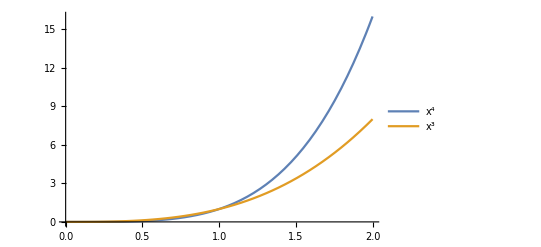

```mathematica
(*Problem 6*)
Plot[{x^4, x^3}, {x, 0, 2}, PlotLegends -> "Expressions"]
```

ClearAll

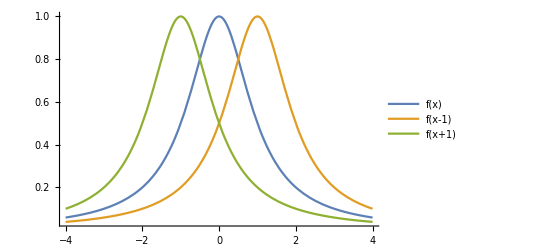

```mathematica
(*Problem 7*)
ClearAll
f[x_]:=1/(1+x^2)
Show[Plot[{f[x], f[x-1], f[x+1]}, {x, -4, 4}, PlotLegends -> "Expressions"], PlotRange -> All]
```

```mathematica
(*Problem8*)
ClearAll
Solve[x^3 == x+1, x, Cubics -> True]
```

ClearAll

{{x→1/3 (27/2-(3 √69)/2)^(1/3)+(1/2 (9+√69))^(1/3)/3^(2/3)},{x→-1/6 (1+ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1-ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))},{x→-1/6 (1-ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1+ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))}}

```mathematica
NSolve[x^3 == x+1, x, Reals]
```

{{x→1.32472}}

```mathematica
(*Problem 9*)
```

```mathematica
Solve[{x+y+z ==z, x-y+z==1, x^2 +y^2 + z^2 ==2}]
```

{{x→1/6 (2-√10),y→1/6 (-2+√10),z→1/3 (1+√10)},{x→1/6 (2+√10),y→1/6 (-2-√10),z→1/3 (1-√10)}}

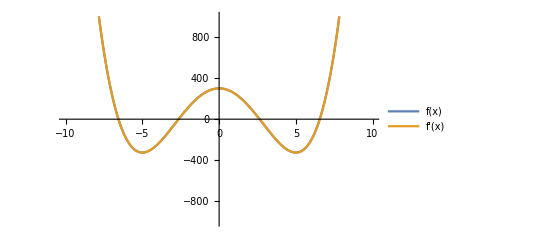

```mathematica
(*Problem 10*)
f[x_]:= x^4 -50x^2 +300
Plot[{f[x], D[f[x]]}, {x, -10, 10}, PlotLegends->{"f(x)", "f'(x)"}, PlotRange->{-1000, 1000}]
```

```mathematica
(*Problem 11*)
ClearAll
f[x_]:= 2x^2
g[x_]:=-x^2 +10
sol =x/.NSolve[f[x]==g[x], x]
```

ClearAll

{-1.82574,1.82574}

```mathematica
Integrate[x^2+10, {x, -1.82574, 1.82574}]
```

40.572

```mathematica
(*Problem 12*)
(*Part 2*)
ClearAll
equ = f3'[x] == x*f3[x]
sol = DSolve[{equ, f3[1]==2}, f3[x], x]
```

ClearAll

f3'[x]==x f3[x]

{{f3[x]→2 ⅇ^(-1/2+x^2/2)}}

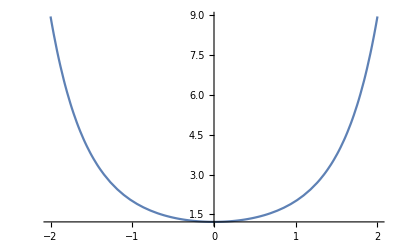

```mathematica
Plot[f3[x]/.sol[[1]], {x, -2, 2}]
```

```mathematica
(*Problem 13*)
A = {{1, 0, 5}, {6, 2, 0}, {1, 0, 3}}
B = {{0, -2, 5}, {2, -7, 8}, {5, -8, 6}}
MatrixForm[A]
```

{{1,0,5},{6,2,0},{1,0,3}}

{{0,-2,5},{2,-7,8},{5,-8,6}}

(1 | 0 | 5
6 | 2 | 0
1 | 0 | 3)

```mathematica
MatrixForm[B]
```

(0 | -2 | 5
2 | -7 | 8
5 | -8 | 6)

```mathematica
Eigenvalues[A]
```

{2+√6,2,2-√6}

```mathematica
Eigenvectors[A]
```

{{-1+√6,6-√6,1},{0,1,0},{-1-√6,6+√6,1}}

```mathematica
Eigenvalues[B]
```

{-2+3 ⅈ,-2-3 ⅈ,3}

```mathematica
Eigenvectors[B]
```

{{-ⅈ,1-ⅈ,1},{ⅈ,1+ⅈ,1},{1,1,1}}

DSolve::dsfun: 2 x^2 cannot be used as a function.